```mathematica
f[t_]:=Cos[t]
negF[t_] := -Cos[t]
```

```mathematica
abs[t_]:= If[f[t]>0,f[t], -f[t] ]
Plot[f[x],{x,0,1}]
```

```mathematica
kleinTrans[t_] := If[f[t]>0,
f[t], 
Log[Cos[t/2]]-Log[Sin[t/2]]]
```

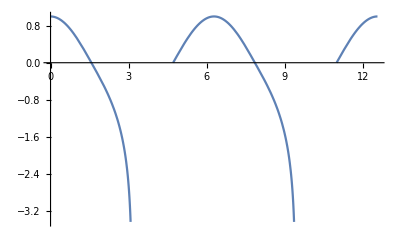

```mathematica
Plot[kleinTrans[t], {t, 0, 4Pi}]
```

```mathematica
Integrate[-1/negF'[t],t]
```

Log[Cos[t/2]]-Log[Sin[t/2]]

```mathematica
-1/negF'[t]
```

-Csc[t]